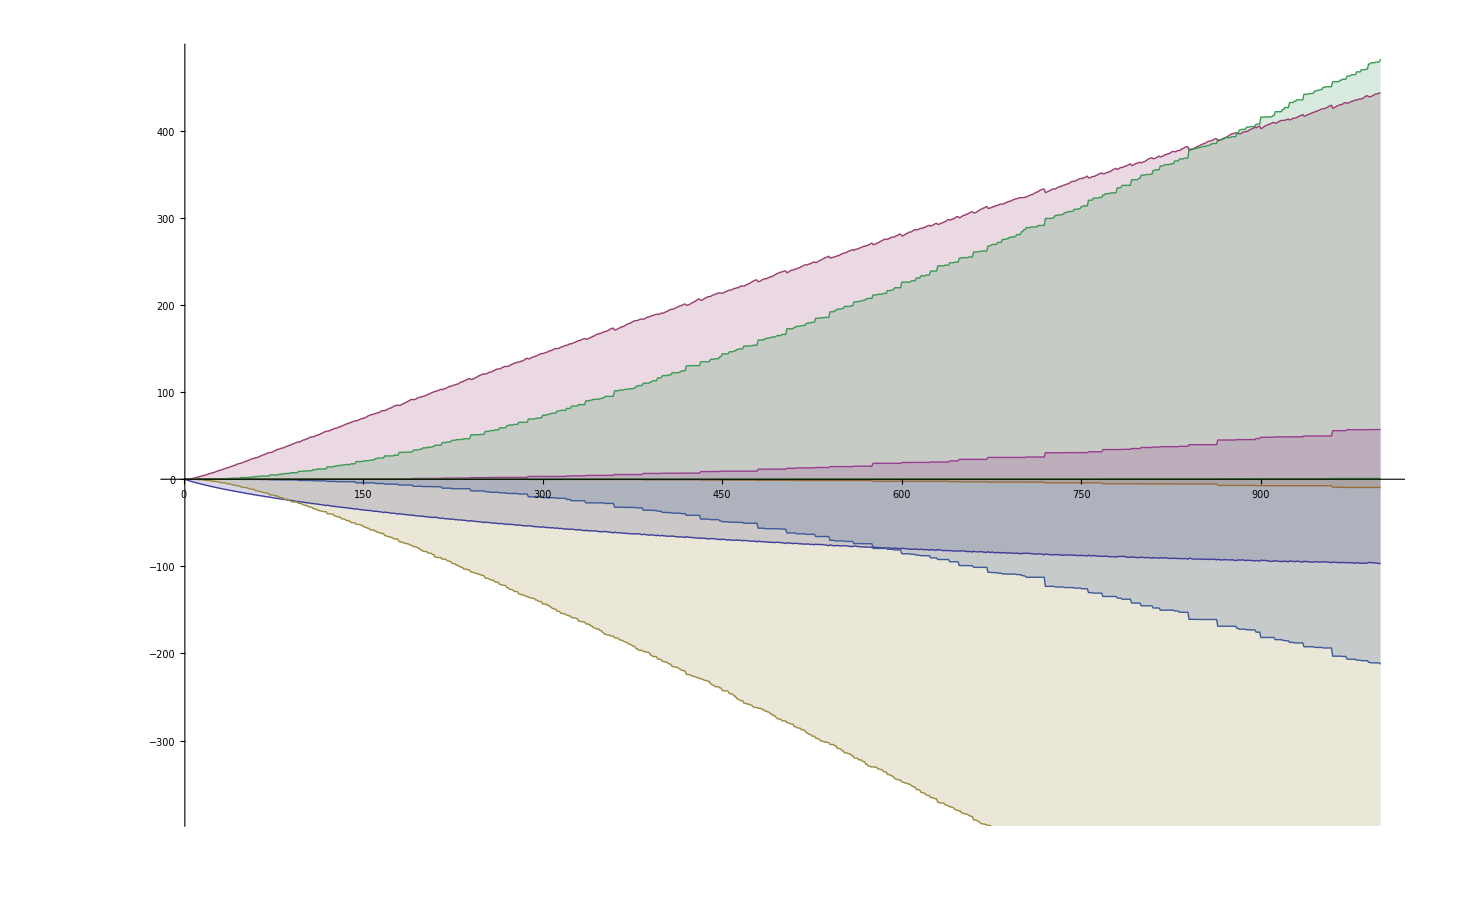

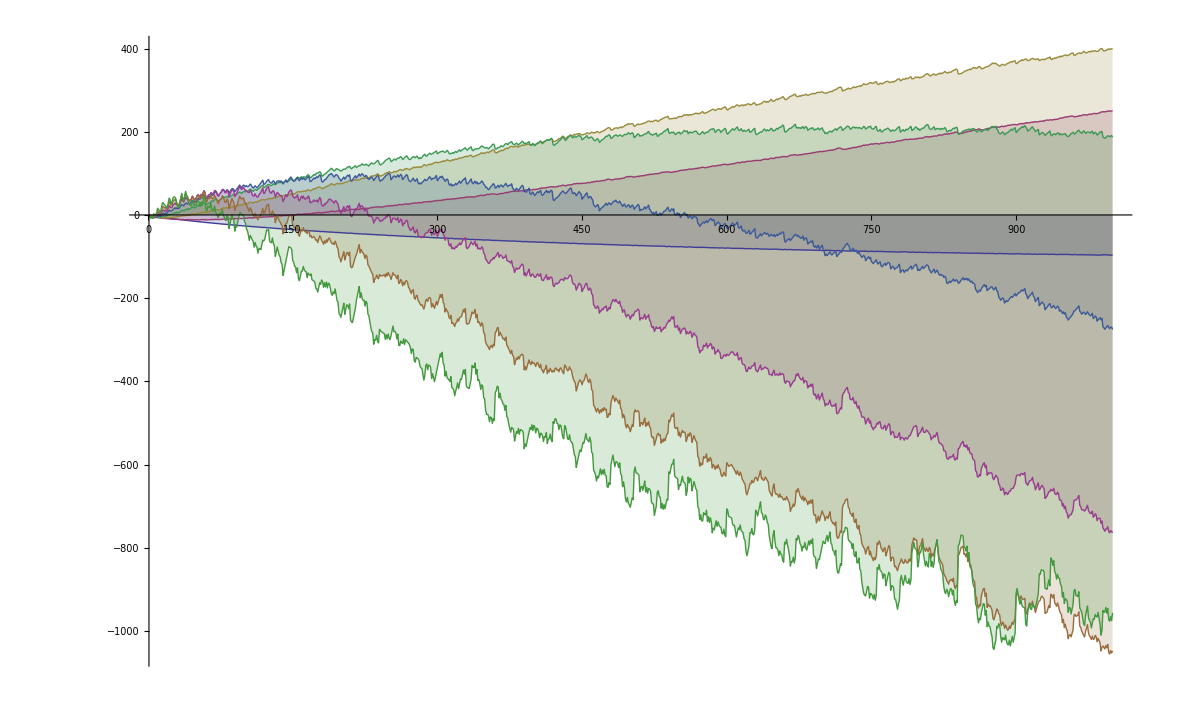

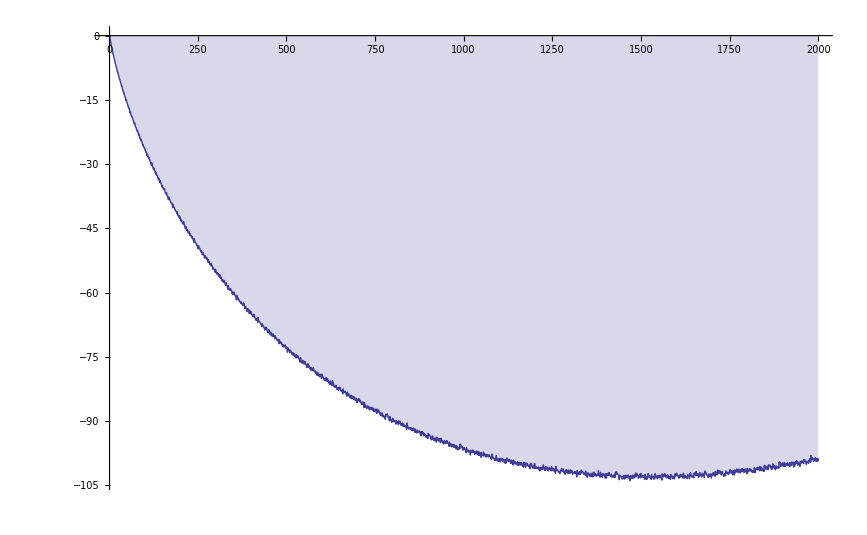

```mathematica
ClearAll["Global`*"]
d2[n_,k_]:=d2[n,k]=Sum[d2[j,k-1] d2[n/j,1],{j,Divisors[n]}];d2[n_,1]:=1;d2[1,1]:=0;d2[n_,0]:=0;d2[1,0]:=1
D2[n_,k_]:=D2[n,k]=D2[n-1,k]+d2[n,k];D2[1,k_]:=0
K[n_]:=K[n]=FullSimplify[MangoldtLambda[n]/Log[n]]
k2[n_,k_]:=k2[n,k]=Sum[k2[j,k-1] k2[n/j,1],{j,Divisors[n]}];k2[n_,1]:=K[n];k2[1,1]:=0;k2[n_,0]:=0;k2[1,0]:=1
K2[n_,k_]:=K2[n,k]=K2[n-1,k]+k2[n,k];K2[1,k_]:=0
e2[n_,1]:=e2[n,1]=Sum[  BernoulliB[k]/(k!) d2[n,k],{k,0,Log[2,n]}];e2[1,1]:=0;
e2[n_,k_]:=Sum[e2[j,k-1]e2[n/j,1],{j,Divisors[n]}];e2[n_,0]:=0;e2[1,0]:=1
E2[n_,k_] := E2[n,k] = E2[n-1,k]+e2[n,k];E2[1,k_]:=0
E1[n_,k_] := Sum[ Binomial[k,j] E2[n,j],{j,0,k}]
DiscretePlot[ {E2[n,1],E2[n,2],E2[n,3],E2[n,4],E2[n,5],E2[n,6],E2[n,7],E2[n,8]},{n,1,1000}]
DiscretePlot[ {E1[n,1],E1[n,2],E1[n,3],E1[n,4],E1[n,5],E1[n,6],E1[n,7],E1[n,8]},{n,1,1000}]
DiscretePlot[ {E1[n,1]},{n,1,2000}]
```

```mathematica
N[E2[2000,1]]
```

360.133

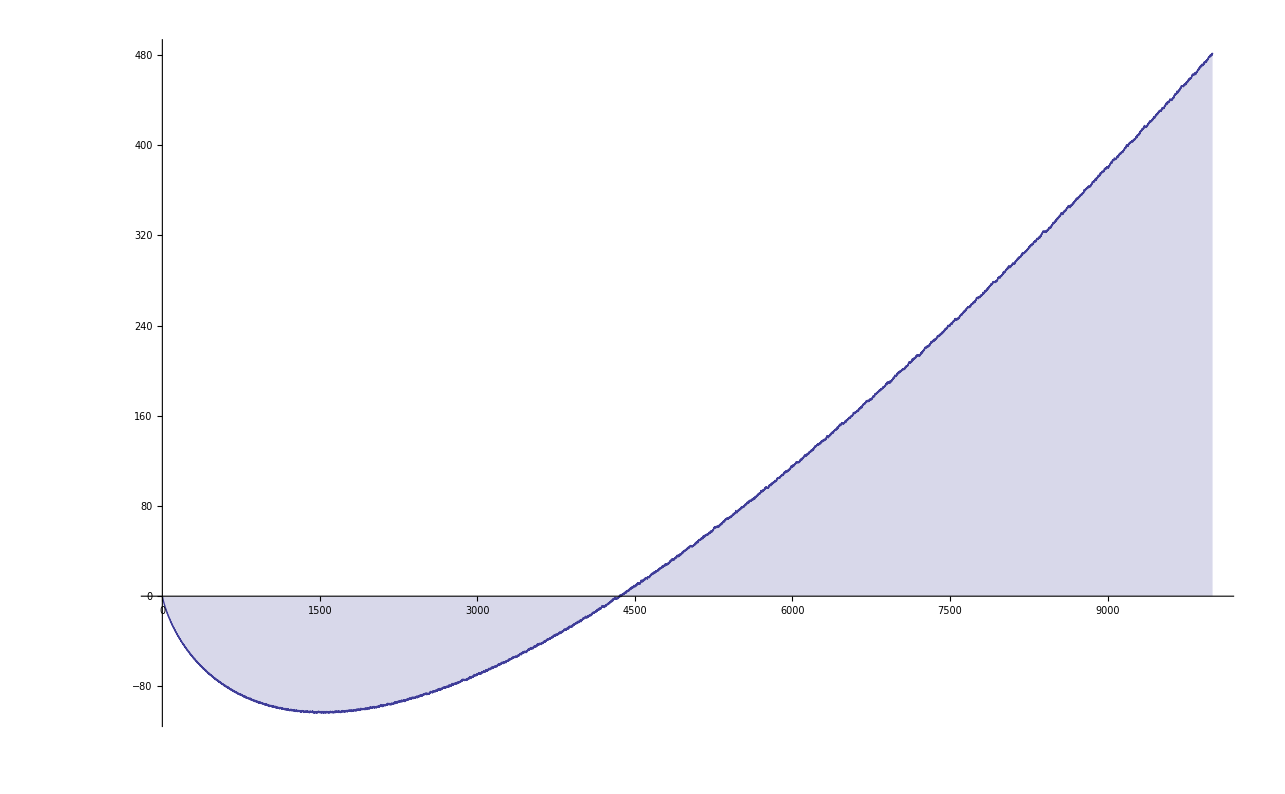

```mathematica
DiscretePlot[ {E1[n,1]},{n,1,10000}]
```